## Para un n fija

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
Res=1*10^(-13);
```

```mathematica
ψn[n_,ρ_]:= ρ*SphericalBesselJ[n,ρ]
```

```mathematica
ξn[n_,ρ_]:=ρ*SphericalHankelH1[n,ρ]
```

```mathematica
dψn[n_,ρ_]:=-n *SphericalBesselJ[n,ρ]+ ρ * SphericalBesselJ[n-1,ρ] 
dξn[n_,ρ_]:=-n * SphericalHankelH1[n,ρ] + ρ* SphericalHankelH1[n-1,ρ]
```

nm : índice de refracción del medio
a : radio de la partícula
ω : frecuencia angular
ωp : frecuencia de plasma
γ : constante de amortiguamiento

nm = 1, A = a ωp/c , W= ω/ ωp, G= γ/ωp = 10^-2

```mathematica
nm=1;
G= 10*^-2;
```

```mathematica
mieSeccTrans[A_,W_,n_]:=Module[{np,m,x,an,bn,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x]));
bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[an]^2+Norm[bn] ^2));
Qext =(2)/(W A)^2*((2 n +1)Re[an+ bn]);

{an,bn,Qsca,Qext}]
```

## Cálculos

### Modelo de Drude

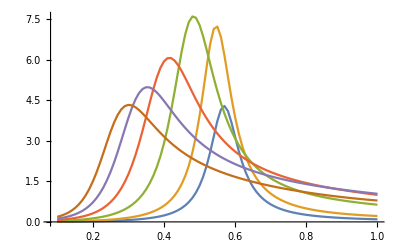

```mathematica
result2=Table[{W,mieSeccTrans[#,W,1][[4]]},{W,0.1,1,0.01}]&/@{5*(13.142/ℏ)/c,10*(13.142/ℏ)/c,20*(13.142/ℏ)/c,30*(13.142/ℏ)/c,40*(13.142/ℏ)/c,50*(13.142/ℏ)/c};
ListLinePlot[result2,AxesLabel->{"",""},PlotRange->All]
```

```mathematica
2.3*(13.142/ℏ)/c
5*(13.142/ℏ)/c
80*(13.142/ℏ)/c
```

0.153074

0.33277

5.32432

```mathematica
GoldenSearchMax[anc_,lower_,upper_,n_]:=Module[{a=N[lower],b=N[upper],c,d},k=0;
While[Abs[(b-(b-a)/GoldenRatio)-(a+(b-a)/GoldenRatio)]>Res,c=(b-(b-a)/GoldenRatio);
d=(a+(b-a)/GoldenRatio);
If[mieSeccTrans[anc,c,n][[4]]>mieSeccTrans[anc,d,n][[4]],(*Then*)b=d(*Else*); k=k+1;,a=c;k++;]];Return[(b+a)/2]];
```

```mathematica
ω1=Table[{anc,GoldenSearchMax[anc,0.1,1,1]},{anc,0.1,8,0.01}];
```

```mathematica
ω2=Table[{anc,GoldenSearchMax[anc,0.1,1,2]},{anc,0.1,8,0.01}];
```

```mathematica
ω3=Table[{anc,GoldenSearchMax[anc,0.1,1,3]},{anc,0.1,8,0.01}];
```

```mathematica
ω4=Table[{anc,GoldenSearchMax[anc,0.1,0.7,4]},{anc,0.1,8,0.01}];
```

```mathematica
ω5=Table[{anc,GoldenSearchMax[anc,0.1,0.7,5]},{anc,0.1,8,0.01}];
```

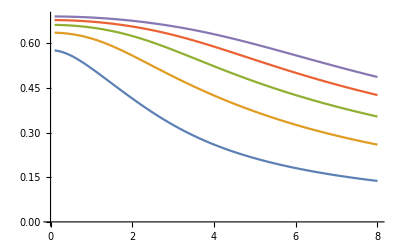

```mathematica
ListLinePlot[{ω1,ω2,ω3,ω4,ω5},PlotRange->All]
```

```mathematica
mieSeccTransBn[A_,W_,n_]:=Module[{np,m,x,bn,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[bn] ^2));
Qext =(2)/(W A)^2*((2 n +1)Re[bn]);

{bn,Qsca,Qext}]
```

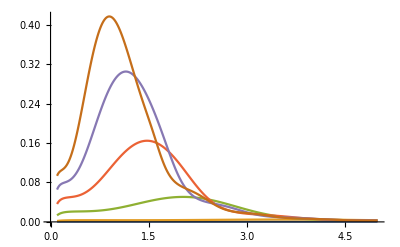

```mathematica
resultBn=Table[{W,mieSeccTransBn[#,W,1][[3]]},{W,0.1,5,0.01}]&/@{5*(13.142/ℏ)/c,10*(13.142/ℏ)/c,20*(13.142/ℏ)/c,30*(13.142/ℏ)/c,40*(13.142/ℏ)/c,50*(13.142/ℏ)/c};
ListLinePlot[resultBn,AxesLabel->{"",""},PlotRange->All]
```

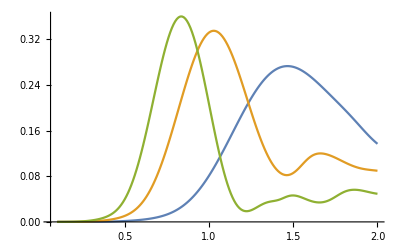

```mathematica
resultBn2=Table[{W,mieSeccTransBn[#,W,4][[3]]},{W,0.1,2,0.01}]&/@{5,6.7,8};
ListLinePlot[resultBn2,AxesLabel->{"",""},PlotRange->All]
```

```mathematica
resBn=10^{-9};
```

```mathematica
GoldenSearchMaxBn[anc_,lower_,upper_,n_]:=Module[{a=N[lower],b=N[upper],c,d},k=0;
While[Abs[(b-(b-a)/GoldenRatio)-(a+(b-a)/GoldenRatio)]>Res,c=(b-(b-a)/GoldenRatio);
d=(a+(b-a)/GoldenRatio);
If[mieSeccTransBn[anc,c,n][[3]]>mieSeccTransBn[anc,d,n][[3]],(*Then*)b=d(*Else*); k=k+1;,a=c;k++;]];Return[(b+a)/2]];
```

```mathematica
GoldenSearchMaxBn[0.1,0.1,5,1]
```

1.62565

```mathematica
ω1Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,5,1]},{anc,0.1,4.97,0.01}];
ω12Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,0.7,1]},{anc,4.98,8,0.01}];
```

```mathematica
ω2Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,10,2]},{anc,0.4,8,0.01}];
```

```mathematica
ω3Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,8,3]},{anc,0.4,8,0.01}];
```

```mathematica
ω4Bn=Table[{anc,GoldenSearchMaxBn[anc,0.05,9,4]},{anc,0.4,8,0.01}];
```

```mathematica
ω5Bn=Table[{anc,GoldenSearchMaxBn[anc,0.05,9,5]},{anc,0.4,8,0.01}];
```

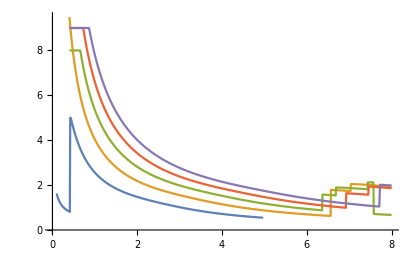

```mathematica
ListLinePlot[{ω1Bn,ω2Bn,ω3Bn,ω4Bn,ω5Bn},AxesLabel->{"",""},PlotRange->All]
```